```mathematica
SetDirectory[NotebookDirectory[]]
(** include the package proj2helpers which contains
Tons and MakePoints **)
Import["proj2helpers.m"];
```

/home/jlmayfield/MonmCourses/COMP161/src

```mathematica
(* 5 sizes *)
sizes = {10,50,100,500,1000,5000,10000,25000,50000,50000,100000,150000,200000,250000};
(* let's assume 6 data points (secondss to compute) per size so
our data file should be 5 lines of 6 comma
separated numbers *)
insertdata = Import["inserttimes.csv"];
```

```mathematica
(* To get pretty labels for the time units we need two things
Tons (To nanoseconds), which converts every entry in the table of
seconds to nanosecond units, and TimeUp which converts ns to whatever
the most appropriate unit of time is. TimeUp only works for one number
so we need to double map it (map to each row, then for each to each column).  This can
be done using anonymous functions like TimeUp[#] & *)
dataAsNS = Tons[insertdata];
timelabeleddata = Map[Map[TimeUp,#]&,dataAsNS]
TableForm[timelabeleddata];
```

{205. ns,42. ns,45. ns,45. ns,45. ns,46. ns}

{{205. ns,42. ns,45. ns,45. ns,45. ns,46. ns},{115. ns,45. ns,45. ns,45. ns,45. ns,42. ns},{470. ns,99. ns,63. ns,105. ns,109. ns,99. ns},{201. ns,232. ns,109. ns,187. ns,220. ns,226. ns},{415. ns,288. ns,295. ns,180. ns,172. ns,394. ns},{366. ns,499. ns,331. ns,286. ns,298. ns,548. ns},{599. ns,301. ns,562. ns,508. ns,433. ns,804. ns},{897. ns,635. ns,731. ns,812. ns,611. ns,1.071 µs},{1.041 µs,643. ns,966. ns,689. ns,1.049 µs,1.401 µs},{1.345 µs,872. ns,957. ns,749. ns,1.128 µs,1.654 µs},{957. ns,1.582 µs,1.405 µs,1.299 µs,1.371 µs,2.15 µs},{1.065 µs,1.645 µs,1.389 µs,1.435 µs,1.516 µs,2.514 µs},{1.63 µs,2.214 µs,1.66 µs,2.37 µs,2.105 µs,2.953 µs},{1.694 µs,2.154 µs,1.853 µs,1.762 µs,2.451 µs,3.404 µs}}

{{Real,Real,Real,Real,Real,Real},{Real,Real,Real,Real,Real,Real},{Real,Real,Real,Real,Real,Real},{Real,Real,Real,Real,Real,Real},{Real,Real,Real,Real,Real,Real},{Real,Real,Real,Real,Real,Real},{Real,Real,Real,Real,Real,Real},{Real,Real,Real,Real,Real,Real},{Real,Real,Real,Real,Real,Real},{Real,Real,Real,Real,Real,Real},{Real,Real,Real,Real,Real,Real},{Real,Real,Real,Real,Real,Real},{Real,Real,Real,Real,Real,Real},{Real,Real,Real,Real,Real,Real}}

```mathematica
isortdata = Import["inserttimes.csv"];
isortSizes = isortdata[[1]]
isortTImes = isortdata[[2;;]]
```

```mathematica
maxPerSize = Map[Max,isortTImes];
TableForm[maxPerSize];
isorttimeNS  = Tons[isortTImes];
TableForm[Map[TimeUp,Map[Max,isorttimeNS]]]
```

1.151 µs
24.445 µs
95.854 µs
2.83415 ms
10.2084 ms
253.554 ms
989.746 ms
6.19077 s
25.2716 s
56.2592 s
1.65754 min
3.68665 min
6.5472 min
9.92718 min

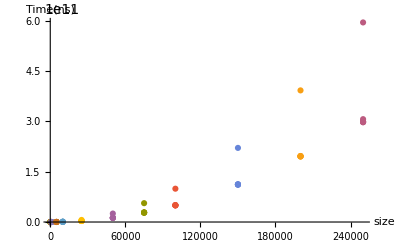

```mathematica
isortPoints = MakePoints[isortSizes,isorttimeNS];
isortgraph = ListPlot[isortPoints,PlotRange->All,AxesLabel->{"size","Time(ns)"}]
```

```mathematica
Export["isortpoints.png",isortgraph, ImageSize -> Large]
```

isortpoints.png